```mathematica
(* A.1 Phase Portrait *)
```

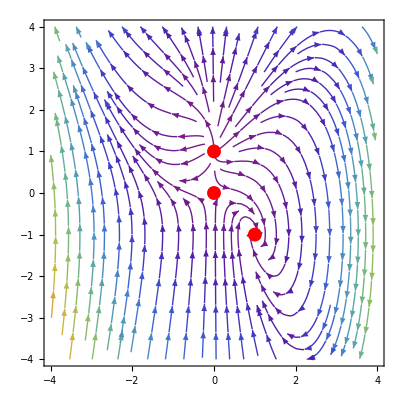

```mathematica
splot=StreamPlot[{x+x y,-y+y^2+x y -x^3},{x,-4,4},{y,-4,4},StreamColorFunction->"Rainbow",Epilog->{Red,PointSize[0.025],Point[{{0,1},{0,0},{1,-1}}]}]
```

```mathematica
(* A.2 Phase Portrait *)
```

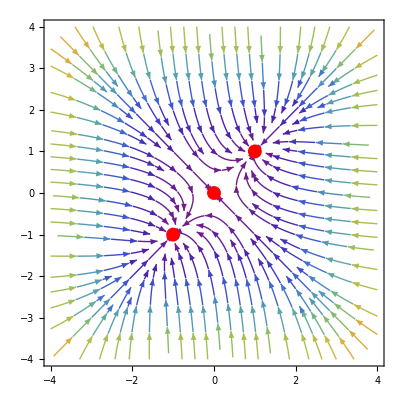

```mathematica
splot=StreamPlot[{-x^3+y,x -y^3},{x,-4,4},{y,-4,4},StreamColorFunction->"Rainbow",Epilog->{Red,PointSize[0.025],Point[{{1,1},{0,0},{-1,-1}}]}]
```

```mathematica
(* A.3 Phase Portrait *)
```

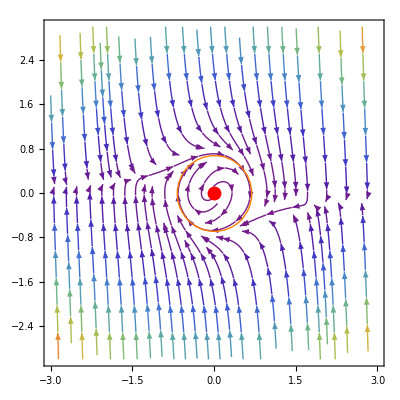

```mathematica
splot=StreamPlot[{y,-x+y(1-3x^2-2y^2)},{x,-3,3},{y,-3,3},StreamColorFunction->"Rainbow",Epilog->{Red,PointSize[0.025],Point[{{0,0}}],Orange,Circle[{0,0},(1+√3)/4]}]
```

```mathematica
A/.{x1->1/(a+1),x2->1/(a+1)}//Simplify//Eigenvalues
```

{(-1-b-√(1-2 b-4 a b+b^2))/(2 (1+a)),(-1-b+√(1-2 b-4 a b+b^2))/(2 (1+a))}

```mathematica
(*A.2.(a)*)
```

```mathematica
Manipulate[StreamPlot[{x(1-x-a y),b y(x-y)},{x,-4,4},{y,-4,4},StreamColorFunction->"Rainbow",StreamPoints->Fine,Epilog->{Point[{0,0}]}],{a,0.1,10,0.1},{b,0.1,10,0.1}]
```

```mathematica
(*A.2.(b)*)
```

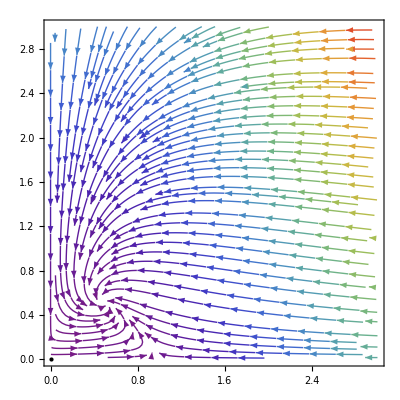

```mathematica
StreamPlot[{x(1-x- y),0.5 y(x-y)},{x,0,3},{y,0,3},StreamColorFunction->"Rainbow",StreamPoints->Fine,Epilog->{Point[{0,0}]}]
```

```mathematica
(*B.2*)
```

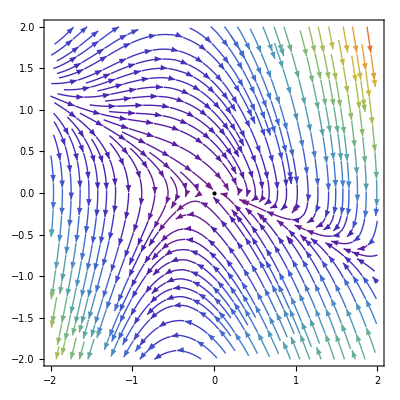

```mathematica
StreamPlot[{y,-y-x^2-2x y},{x,-2,2},{y,-2,2},StreamColorFunction->"Rainbow",StreamPoints->Fine,Epilog->{Point[{0,0}]}]
```

```mathematica
(*B.3 μ=0*)
```

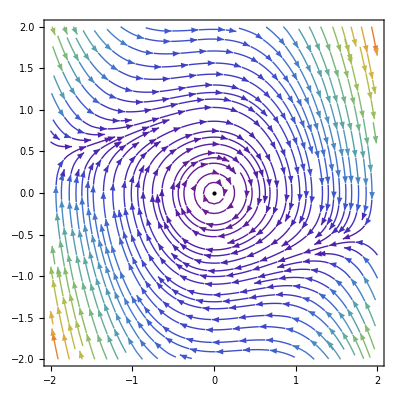

```mathematica
StreamPlot[{y,-x-x^2 y},{x,-2,2},{y,-2,2},StreamColorFunction->"Rainbow",StreamPoints->Fine,Epilog->{Point[{0,0}]}]
```

```mathematica
(*B.3 μ=-0.1*)
```

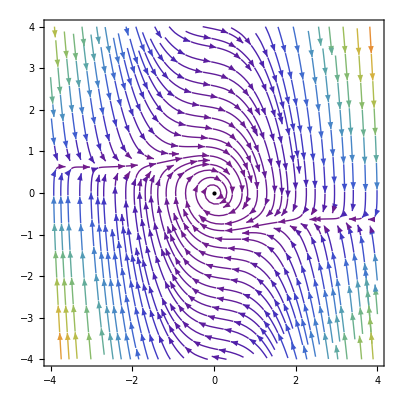

```mathematica
StreamPlot[{y,-1.01x-0.2y-0.1x^3-x^2 y},{x,-4,4},{y,-4,4},StreamColorFunction->"Rainbow",StreamPoints->Fine,Epilog->{Point[{0,0}]}]
```

```mathematica
(*B.3 μ=0.1*)
```

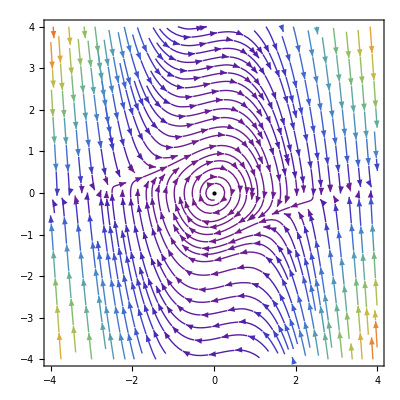

```mathematica
StreamPlot[{y,-1.01x+0.2y+0.1x^3-x^2 y},{x,-4,4},{y,-4,4},StreamColorFunction->"Rainbow",StreamPoints->Fine,Epilog->{Point[{0,0}]}]
```

```mathematica
Eigenvalues[{{0,1},{2m,-1+2m}}]
```

{-1,2 m}